```mathematica
f[x_,y_]:=x^2+3(y-1)^2+x y+3 Sign[x]
```

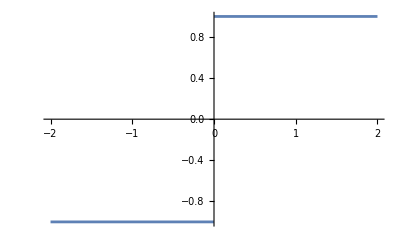

```mathematica
Plot[Sign[x],{x,-2,2}]
```

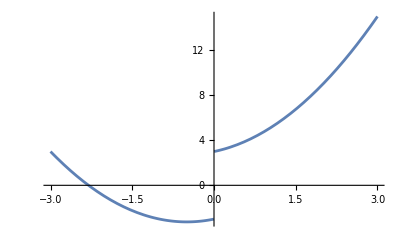

```mathematica
Plot[f[x,1],{x,-3,3},PlotRange->All]
```

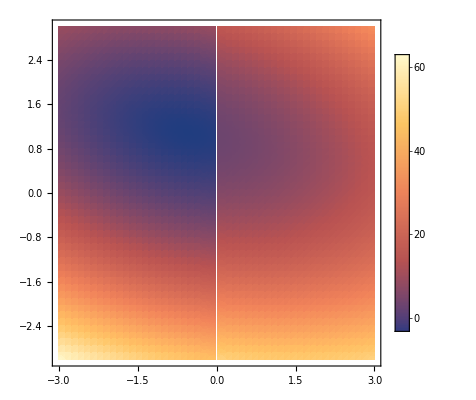

```mathematica
DensityPlot[f[x,y],{x,-3,3},{y,-3,3},PlotRange->All,PlotPoints->50,PlotLegends->Automatic]
```

```mathematica
NMinimize[{f[x,y],-5<x<5,-5<y<5},{x,y}]
```

{-3.27273,{x→-0.545455,y→1.09091}}

```mathematica
(*NMinimze can deal with all kinds of constraints etc. It internally chooses teh rigth algorithm.*)
```

f should now be your cost function, e . g . r1 and r2 are the tunneling ratios, and we want r10  and r20 , and the flux is xi and xi0, then you can try  f=a (r1-r10)^2+b (r2-r20)^2+c (φ-φ0 )^2 and play with a,b,c to optimise...

```mathematica
(* Define J23 tunnelling val*)
J23[A2_, A3_, omega_, phi3_]:= (omega/2/π)*NIntegrate[Cos[A3/2/omega*Sin[2*omega*t+phi3]-A2/omega*Sin[omega*t]],{t,-π/omega,π/omega}]+(omega*ⅈ/2/π)*NIntegrate[Sin[A3/2/omega*Sin[2*omega*t+phi3]-A2/omega*Sin[omega*t]],{t, -π/omega,π/omega}]
(* define flux xi*)
Xi[A2_, A3_, omega_, phi3_]:=Arg[BesselJ[0,A3/2/omega]*BesselJ[0,A2/omega]*J23[A2, A3, omega, phi3]]
(*Define function to retrieve middle value of 3x1 list *)
Mid[v1_, v2_, v3_]:=v1+v2+v3-Max[v1, v2, v3] - Min[v1, v2, v3]
(*define tunnelling ratios*)
R1[A2_, A3_, omega_, phi3_]:= Mid[ Abs[ BesselJ[0,A3/2/omega]],Abs[J23[A2, A3, omega, phi3]], Abs[BesselJ[0,A2/omega]]]/Max[Abs[ BesselJ[0,A3/2/omega]],Abs[J23[A2, A3, omega, phi3]], Abs[BesselJ[0,A2/omega]]]
R2[A2_, A3_ ,omega_, phi3_]:=Min[ Abs[ BesselJ[0,A3/2/omega]],Abs[J23[A2, A3, omega, phi3]], Abs[BesselJ[0,A2/omega]]]/Max[Abs[ BesselJ[0,A3/2/omega]],Abs[J23[A2, A3, omega, phi3]], Abs[BesselJ[0,A2/omega]]]

r10= 0.9; (*x val on rel triangle *)
r20 = 0.7; (* y val on rel triangle *)

(*func to minimise*)
f[A2_, A3_, omega_, phi3_, r10_, r20_, xi0_, a_, b_, c_]:= a*(Xi[A2, A3, omega, phi3]- xi0)^2 + b*(R1[A2, A3, omega, phi3] - r10)^2+ c*(R2[A2, A3, omega, phi3] - r20)^2
```

```mathematica
Export["//wsl.localhost/Ubuntu/home/gnixon/floquet-simulations/paper_data/" <>filename,dataTable];
```

StringJoin::string: String expected at position 2 in //wsl.localhost/Ubuntu/home/gnixon/floquet-simulations/paper_data/<>filename.

Export::chtype: First argument //wsl.localhost/Ubuntu/home/gnixon/floquet-simulations/paper_data/<>filename is not a valid file specification.

```mathematica
Export["//wsl.localhost/Ubuntu/home/gnixon/floquet-simulations/paper_data/" <>filename,dataTable];
```

#### try import initial conditions

```mathematica
filename = "initial_conditions.csv";
initialConds= Import["//wsl.localhost/Ubuntu/home/gnixon/floquet-simulations/paper_data/" <>filename,"Data", HeaderLines->1, Delimiters->","];
initialA2s = initialConds[[All,5]];
initialA3s = initialConds[[All,6]];
initialVarphis = initialConds[[All,8]];
initialXi0Fracs = initialConds[[All,3]];
r10 = initialConds[[1,1]]
r20 = initialConds[[1,2]]
```

0.5

0.3

```mathematica
(*Target params*)
(*dataTable = {{"algo", "r10", "r20", "xi0", "a", "b", "c", "A2", "A3", "omega", "phi", "error", "A2_ic", "A3_ic", "omega_ic", "varphi_frac_ic"}};*)
filename = "continuous_neighbourhood_grad_descent_findminimum_initial_conds.csv";
dataTable = Import["//wsl.localhost/Ubuntu/home/gnixon/floquet-simulations/paper_data/" <>filename,"Data"];
a = 1; b = 10; c = 10;

Nvals = 50;
For[ii = 1, ii≤ Nvals, ii++,
Print[ii,", ", initialXi0Fracs [[ii]],", ",  initialA2s[[ii]], ", ",  initialA3s[[ii]],", ",  initialVarphis[[ii]]];
(*Do minimisation*)
xi0= initialXi0Fracs[[ii]]*π; 
(*sol = NMinimize[{f[A2, A3, omega, phi3, r10, r20, xi0, a, b, c], 0<A2<70,0<A3<70, 8 < omega, 0≤phi3<2*π},{A2, A3, omega, phi3}];
sol = NMinimize[{f[A2, A3,  omegaI, phi3, r10, r20, xi0, a, b, c], 0<A2<70,0<A3<70, 0≤phi3<2*π},{A2, A3,  phi3}];*)
sol = FindMinimum[{f[A2, A3, omega, phi3, r10, r20, xi0, a, b, c], 0<A2<70,0<A3<70, 7.9<= omega, -2*Pi≤phi3<2*π},
 {{A2,initialA2s[[ii]]},{A3,initialA3s[[ii]]}, {omega,8}, {phi3,initialVarphis[[ii]]*Pi}},
PrecisionGoal->4,
AccuracyGoal->4,
MaxIterations->Infinity
];

errorc = sol[[1]];
A2c = sol[[2,1,2]];
A3c = sol[[2,2,2]];
omegac = sol[[2,3,2]];
phic = sol[[2,4,2]];
Print["                           ", A2c,", ",  A3c ", ",  omegac,", ", phic, ", ", errorc];
dataTable = Append[dataTable, {"FindMinimum,PG=4,AG=4,MI=inf,imported_ic_smart4.0", r10,r20, xi0/Pi, a, b, c, A2c, A3c, omegac, phic, errorc, initialA2s[[ii]], initialA3s[[ii]], 8, initialVarphis[[ii]]}];
]
Export["//wsl.localhost/Ubuntu/home/gnixon/floquet-simulations/paper_data/" <>filename,dataTable];
```

1, 0., 33., 16., 2.

FindMinimum::nrnum: The function value f[33.,16.,8.,6.28319,0.5,0.3,0.,1,10,10] is not a real number at {A2,A3,omega,phi3} = {33.,16.,8.,6.28319}.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

FindMinimum::nrnum: The function value f[32.9998,16.,8.,6.28319,0.5,0.3,0.,1,10,10] is not a real number at {A2,A3,omega,phi3} = {32.9998,16.,8.,6.28319}.

FindMinimum::nrnum: The function value f[32.9998,16.,8.,6.28219,0.5,0.3,0.,1,10,10] is not a real number at {A2,A3,omega,phi3} = {32.9998,16.,8.,6.28219}.

General::stop: Further output of FindMinimum::nrnum will be suppressed during this calculation.

FindMinimum::grad: Evaluation of the gradient of function Experimental`NumericalFunction[{Hold[f[A2,A3,omega,phi3,0.5,0.3,0.,1,10,10]],Block},{0,{{{},1,0,Hold[A2],0,0},{{},1,1,Hold[A3],0,0},{{},1,2,Hold[omega],0,0},{{},1,3,Hold[phi3],0,0}}},{{{1,4,817},{{Automatic,Automatic,None,2,Automatic},{}}}},{8,3,{},0},{904,MachinePrecision,{{Automatic},{Hold[f[A2,A3,omega,phi3,0.5,0.3,0.,1,10,10]],Block}},True,{{Automatic,CleanUpRegisters→False,WarningMessages→False,EvaluateSymbolically→False,RuntimeErrorHandler→($Failed&)},{},Automatic,WVM},FindMinimum,Automatic,None},{None,None,None}] failed at {33.,16.,8.,6.28219}.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

FindMinimum::grad: Evaluation of the gradient of function Experimental`NumericalFunction[{Hold[f[A2,A3,omega,phi3,0.5,0.3,0.,1,10,10]],Block},{0,{{{},1,0,Hold[A2],0,0},{{},1,1,Hold[A3],0,0},{{},1,2,Hold[omega],0,0},{{},1,3,Hold[phi3],0,0}}},{{{1,4,817},{{Automatic,Automatic,None,2,Automatic},{}}}},{8,3,{},0},{904,MachinePrecision,{{Automatic},{Hold[f[A2,A3,omega,phi3,0.5,0.3,0.,1,10,10]],Block}},True,{{Automatic,CleanUpRegisters→False,WarningMessages→False,EvaluateSymbolically→False,RuntimeErrorHandler→($Failed&)},{},Automatic,WVM},FindMinimum,Automatic,None},{None,None,None}] failed at {33.,16.,8.,6.28219}.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

General::stop: Further output of IPOPTMinimize::badobj will be suppressed during this calculation.

FindMinimum::grad: Evaluation of the gradient of function Experimental`NumericalFunction[{Hold[f[A2,A3,omega,phi3,0.5,0.3,0.,1,10,10]],Block},{0,{{{},1,0,Hold[A2],0,0},{{},1,1,Hold[A3],0,0},{{},1,2,Hold[omega],0,0},{{},1,3,Hold[phi3],0,0}}},{{{1,4,817},{{Automatic,Automatic,None,2,Automatic},{}}}},{8,3,{},0},{904,MachinePrecision,{{Automatic},{Hold[f[A2,A3,omega,phi3,0.5,0.3,0.,1,10,10]],Block}},True,{{Automatic,CleanUpRegisters→False,WarningMessages→False,EvaluateSymbolically→False,RuntimeErrorHandler→($Failed&)},{},Automatic,WVM},FindMinimum,Automatic,None},{None,None,None}] failed at {33.,16.,8.,6.28219}.

General::stop: Further output of FindMinimum::grad will be suppressed during this calculation.

33., 16. , 8, 6.28319, {f[A2,A3,omega,phi3,0.5,0.3,0.,1,10,10],0<A2<70,0<A3<70,7.9≤omega,-2 π≤phi3<2 π}

2, 0.02, 33., 16., 1.98

33., 16. , 8, 6.22035, {f[A2,A3,omega,phi3,0.5,0.3,0.0628319,1,10,10],0<A2<70,0<A3<70,7.9≤omega,-2 π≤phi3<2 π}

3, 0.04, 33., 15., 1.96

33., 15. , 8, 6.15752, {f[A2,A3,omega,phi3,0.5,0.3,0.125664,1,10,10],0<A2<70,0<A3<70,7.9≤omega,-2 π≤phi3<2 π}

4, 0.06, 33., 16.5, 1.96

33., 16.5 , 8, 6.15752, {f[A2,A3,omega,phi3,0.5,0.3,0.188496,1,10,10],0<A2<70,0<A3<70,7.9≤omega,-2 π≤phi3<2 π}

5, 0.08, 26.5, 17.5, 1.96

26.5, 17.5 , 8, 6.15752, {f[A2,A3,omega,phi3,0.5,0.3,0.251327,1,10,10],0<A2<70,0<A3<70,7.9≤omega,-2 π≤phi3<2 π}

6, 0.1, 26.5, 19., 1.96

26.5, 19. , 8, 6.15752, {f[A2,A3,omega,phi3,0.5,0.3,0.314159,1,10,10],0<A2<70,0<A3<70,7.9≤omega,-2 π≤phi3<2 π}

7, 0.12, 27., 18., 1.94

27., 18. , 8, 6.09469, {f[A2,A3,omega,phi3,0.5,0.3,0.376991,1,10,10],0<A2<70,0<A3<70,7.9≤omega,-2 π≤phi3<2 π}

8, 0.14, 26.5, 19., 1.94

26.5, 19. , 8, 6.09469, {f[A2,A3,omega,phi3,0.5,0.3,0.439823,1,10,10],0<A2<70,0<A3<70,7.9≤omega,-2 π≤phi3<2 π}

9, 0.16, 26., 20., 1.94

26., 20. , 8, 6.09469, {f[A2,A3,omega,phi3,0.5,0.3,0.502655,1,10,10],0<A2<70,0<A3<70,7.9≤omega,-2 π≤phi3<2 π}

10, 0.18, 26., 18.5, 1.92

26., 18.5 , 8, 6.03186, {f[A2,A3,omega,phi3,0.5,0.3,0.565487,1,10,10],0<A2<70,0<A3<70,7.9≤omega,-2 π≤phi3<2 π}

11, 0.2, 26., 20., 1.92

26., 20. , 8, 6.03186, {f[A2,A3,omega,phi3,0.5,0.3,0.628319,1,10,10],0<A2<70,0<A3<70,7.9≤omega,-2 π≤phi3<2 π}

12, 0.22, 25.5, 20.5, 1.92

25.5, 20.5 , 8, 6.03186, {f[A2,A3,omega,phi3,0.5,0.3,0.69115,1,10,10],0<A2<70,0<A3<70,7.9≤omega,-2 π≤phi3<2 π}

13, 0.24, 25., 21., 1.92

25., 21. , 8, 6.03186, {f[A2,A3,omega,phi3,0.5,0.3,0.753982,1,10,10],0<A2<70,0<A3<70,7.9≤omega,-2 π≤phi3<2 π}

14, 0.26, 25., 22., 1.92

25., 22. , 8, 6.03186, {f[A2,A3,omega,phi3,0.5,0.3,0.816814,1,10,10],0<A2<70,0<A3<70,7.9≤omega,-2 π≤phi3<2 π}

15, 0.28, 24.5, 22.5, 1.92

24.5, 22.5 , 8, 6.03186, {f[A2,A3,omega,phi3,0.5,0.3,0.879646,1,10,10],0<A2<70,0<A3<70,7.9≤omega,-2 π≤phi3<2 π}

16, 0.3, 24., 12.5, 1.58

24., 12.5 , 8, 4.96372, {f[A2,A3,omega,phi3,0.5,0.3,0.942478,1,10,10],0<A2<70,0<A3<70,7.9≤omega,-2 π≤phi3<2 π}

17, 0.32, 23.5, 14., 1.66

23.5, 14. , 8, 5.21504, {f[A2,A3,omega,phi3,0.5,0.3,1.00531,1,10,10],0<A2<70,0<A3<70,7.9≤omega,-2 π≤phi3<2 π}

18, 0.34, 23.5, 16.5, 1.72

23.5, 16.5 , 8, 5.40354, {f[A2,A3,omega,phi3,0.5,0.3,1.06814,1,10,10],0<A2<70,0<A3<70,7.9≤omega,-2 π≤phi3<2 π}

19, 0.36, 23.5, 24.5, 1.92

23.5, 24.5 , 8, 6.03186, {f[A2,A3,omega,phi3,0.5,0.3,1.13097,1,10,10],0<A2<70,0<A3<70,7.9≤omega,-2 π≤phi3<2 π}

20, 0.38, 12.5, 43.5, 1.5

12.5, 43.5 , 8, 4.71239, {f[A2,A3,omega,phi3,0.5,0.3,1.19381,1,10,10],0<A2<70,0<A3<70,7.9≤omega,-2 π≤phi3<2 π}

21, 0.4, 13., 43., 1.38

13., 43. , 8, 4.3354, {f[A2,A3,omega,phi3,0.5,0.3,1.25664,1,10,10],0<A2<70,0<A3<70,7.9≤omega,-2 π≤phi3<2 π}

22, 0.42, 17., 51., 1.14

17., 51. , 8, 3.58142, {f[A2,A3,omega,phi3,0.5,0.3,1.31947,1,10,10],0<A2<70,0<A3<70,7.9≤omega,-2 π≤phi3<2 π}

23, 0.44, 17., 50., 1.12

17., 50. , 8, 3.51858, {f[A2,A3,omega,phi3,0.5,0.3,1.3823,1,10,10],0<A2<70,0<A3<70,7.9≤omega,-2 π≤phi3<2 π}

24, 0.46, 21., 52.5, 0.72

21., 52.5 , 8, 2.26195, {f[A2,A3,omega,phi3,0.5,0.3,1.44513,1,10,10],0<A2<70,0<A3<70,7.9≤omega,-2 π≤phi3<2 π}

25, 0.48, 22.5, 56., 0.64

22.5, 56. , 8, 2.01062, {f[A2,A3,omega,phi3,0.5,0.3,1.50796,1,10,10],0<A2<70,0<A3<70,7.9≤omega,-2 π≤phi3<2 π}

26, 0.5, 22.5, 56., 0.62

22.5, 56. , 8, 1.94779, {f[A2,A3,omega,phi3,0.5,0.3,1.5708,1,10,10],0<A2<70,0<A3<70,7.9≤omega,-2 π≤phi3<2 π}

27, 0.52, 22.5, 56., 0.6

22.5, 56. , 8, 1.88496, {f[A2,A3,omega,phi3,0.5,0.3,1.63363,1,10,10],0<A2<70,0<A3<70,7.9≤omega,-2 π≤phi3<2 π}

28, 0.54, 21., 53.5, 0.62

21., 53.5 , 8, 1.94779, {f[A2,A3,omega,phi3,0.5,0.3,1.69646,1,10,10],0<A2<70,0<A3<70,7.9≤omega,-2 π≤phi3<2 π}

29, 0.56, 21., 53.5, 0.58

21., 53.5 , 8, 1.82212, {f[A2,A3,omega,phi3,0.5,0.3,1.75929,1,10,10],0<A2<70,0<A3<70,7.9≤omega,-2 π≤phi3<2 π}

30, 0.58, 21., 54., 0.5

21., 54. , 8, 1.5708, {f[A2,A3,omega,phi3,0.5,0.3,1.82212,1,10,10],0<A2<70,0<A3<70,7.9≤omega,-2 π≤phi3<2 π}

31, 0.6, 20.5, 37., 1.1

20.5, 37. , 8, 3.45575, {f[A2,A3,omega,phi3,0.5,0.3,1.88496,1,10,10],0<A2<70,0<A3<70,7.9≤omega,-2 π≤phi3<2 π}

32, 0.62, 17., 40., 1.06

17., 40. , 8, 3.33009, {f[A2,A3,omega,phi3,0.5,0.3,1.94779,1,10,10],0<A2<70,0<A3<70,7.9≤omega,-2 π≤phi3<2 π}

33, 0.64, 29.5, 35., 1.12

29.5, 35. , 8, 3.51858, {f[A2,A3,omega,phi3,0.5,0.3,2.01062,1,10,10],0<A2<70,0<A3<70,7.9≤omega,-2 π≤phi3<2 π}

34, 0.66, 30.5, 35., 1.12

30.5, 35. , 8, 3.51858, {f[A2,A3,omega,phi3,0.5,0.3,2.07345,1,10,10],0<A2<70,0<A3<70,7.9≤omega,-2 π≤phi3<2 π}

35, 0.68, 31.5, 35., 1.12

31.5, 35. , 8, 3.51858, {f[A2,A3,omega,phi3,0.5,0.3,2.13628,1,10,10],0<A2<70,0<A3<70,7.9≤omega,-2 π≤phi3<2 π}

36, 0.7, 32., 35., 1.12

32., 35. , 8, 3.51858, {f[A2,A3,omega,phi3,0.5,0.3,2.19911,1,10,10],0<A2<70,0<A3<70,7.9≤omega,-2 π≤phi3<2 π}

37, 0.72, 33., 35., 1.12

33., 35. , 8, 3.51858, {f[A2,A3,omega,phi3,0.5,0.3,2.26195,1,10,10],0<A2<70,0<A3<70,7.9≤omega,-2 π≤phi3<2 π}

38, 0.74, 32., 35., 1.1

32., 35. , 8, 3.45575, {f[A2,A3,omega,phi3,0.5,0.3,2.32478,1,10,10],0<A2<70,0<A3<70,7.9≤omega,-2 π≤phi3<2 π}

39, 0.76, 32.5, 35., 1.1

32.5, 35. , 8, 3.45575, {f[A2,A3,omega,phi3,0.5,0.3,2.38761,1,10,10],0<A2<70,0<A3<70,7.9≤omega,-2 π≤phi3<2 π}

40, 0.78, 33.5, 35., 1.1

33.5, 35. , 8, 3.45575, {f[A2,A3,omega,phi3,0.5,0.3,2.45044,1,10,10],0<A2<70,0<A3<70,7.9≤omega,-2 π≤phi3<2 π}

41, 0.8, 42., 40., 0.74

42., 40. , 8, 2.32478, {f[A2,A3,omega,phi3,0.5,0.3,2.51327,1,10,10],0<A2<70,0<A3<70,7.9≤omega,-2 π≤phi3<2 π}

42, 0.82, 33., 35., 1.08

33., 35. , 8, 3.39292, {f[A2,A3,omega,phi3,0.5,0.3,2.57611,1,10,10],0<A2<70,0<A3<70,7.9≤omega,-2 π≤phi3<2 π}

43, 0.84, 40., 28.5, 1.14

40., 28.5 , 8, 3.58142, {f[A2,A3,omega,phi3,0.5,0.3,2.63894,1,10,10],0<A2<70,0<A3<70,7.9≤omega,-2 π≤phi3<2 π}

44, 0.86, 41., 30.5, 1.18

41., 30.5 , 8, 3.70708, {f[A2,A3,omega,phi3,0.5,0.3,2.70177,1,10,10],0<A2<70,0<A3<70,7.9≤omega,-2 π≤phi3<2 π}

45, 0.88, 39.5, 27.5, 1.1

39.5, 27.5 , 8, 3.45575, {f[A2,A3,omega,phi3,0.5,0.3,2.7646,1,10,10],0<A2<70,0<A3<70,7.9≤omega,-2 π≤phi3<2 π}

46, 0.9, 39.5, 27., 1.08

39.5, 27. , 8, 3.39292, {f[A2,A3,omega,phi3,0.5,0.3,2.82743,1,10,10],0<A2<70,0<A3<70,7.9≤omega,-2 π≤phi3<2 π}

47, 0.92, 32., 32.5, 1.02

32., 32.5 , 8, 3.20442, {f[A2,A3,omega,phi3,0.5,0.3,2.89027,1,10,10],0<A2<70,0<A3<70,7.9≤omega,-2 π≤phi3<2 π}

48, 0.94, 55., 41.5, 1.06

55., 41.5 , 8, 3.33009, {f[A2,A3,omega,phi3,0.5,0.3,2.9531,1,10,10],0<A2<70,0<A3<70,7.9≤omega,-2 π≤phi3<2 π}

49, 0.96, 46.5, 43.5, 1.08

46.5, 43.5 , 8, 3.39292, {f[A2,A3,omega,phi3,0.5,0.3,3.01593,1,10,10],0<A2<70,0<A3<70,7.9≤omega,-2 π≤phi3<2 π}

50, 0.98, 46.5, 44., 1.04

46.5, 44. , 8, 3.26726, {f[A2,A3,omega,phi3,0.5,0.3,3.07876,1,10,10],0<A2<70,0<A3<70,7.9≤omega,-2 π≤phi3<2 π}

```mathematica
Export["//wsl.localhost/Ubuntu/home/gnixon/floquet-simulations/paper_data/" <>filename,dataTable];
```

## Import initial conditions and then set w=8

```mathematica
filename = "initial_conditions.csv";
initialConds= Import["//wsl.localhost/Ubuntu/home/gnixon/floquet-simulations/paper_data/" <>filename,"Data", HeaderLines->1, Delimiters->","];
initialA2s = initialConds[[All,5]];
initialA3s = initialConds[[All,6]];
initialVarphis = initialConds[[All,8]];
initialXi0Fracs = initialConds[[All,3]];
r10=  initialConds[[1, 1]]
r20 = initialConds[[1, 2]]
```

0.5

0.3

```mathematica
(* Define J23 tunnelling val*)
J23w8[A2_, A3_, phi3_]:= (8/2/π)*NIntegrate[Cos[A3/2/8*Sin[2*8*t+phi3]-A2/8*Sin[8*t]],{t,-π/8,π/8}]+(8*ⅈ/2/π)*NIntegrate[Sin[A3/2/8*Sin[2*8*t+phi3]-A2/8*Sin[8*t]],{t, -π/8,π/8}]
(* define flux xi*)
Xiw8[A2_, A3_,  phi3_]:=Arg[BesselJ[0,A3/2/8]*BesselJ[0,A2/8]*J23w8[A2, A3, phi3]]
(*Define function to retrieve middle value of 3x1 list *)
Mid[v1_, v2_, v3_]:=v1+v2+v3-Max[v1, v2, v3] - Min[v1, v2, v3]
(*define tunnelling ratios*)
R1w8[A2_, A3_,  phi3_]:= Mid[ Abs[ BesselJ[0,A3/2/8]],Abs[J23w8[A2, A3, phi3]], Abs[BesselJ[0,A2/8]]]/Max[Abs[ BesselJ[0,A3/2/8]],Abs[J23w8[A2, A3, phi3]], Abs[BesselJ[0,A2/8]]]
R2w8[A2_, A3_ , phi3_]:=Min[ Abs[ BesselJ[0,A3/2/8]],Abs[J23w8[A2, A3, phi3]], Abs[BesselJ[0,A2/8]]]/Max[Abs[ BesselJ[0,A3/2/8]],Abs[J23w8[A2, A3, phi3]], Abs[BesselJ[0,A2/8]]]

(*func to minimise*)
fw8[A2_, A3_,  phi3_, r10_, r20_, xi0_, a_, b_, c_]:= a*(Xiw8[A2, A3,  phi3]- xi0)^2 + b*(R1w8[A2, A3,  phi3] - r10)^2+ c*(R2w8[A2, A3, phi3] - r20)^2
```

```mathematica
(*Target params*)
(*dataTable = {{"algo", "r10", "r20", "xi0", "a", "b", "c", "A2", "A3", "omega", "phi", "error", "A2_ic", "A3_ic", "omega_ic", "varphi_frac_ic"}};*)
filename = "continuous_neighbourhood_grad_descent_findminimum_initial_conds.csv";
dataTable = Import["//wsl.localhost/Ubuntu/home/gnixon/floquet-simulations/paper_data/" <>filename,"Data"];
a = 1; b = 10; c = 10;

Nvals = 50;
For[ii = 1, ii≤ Nvals, ii++,
Print[ii,", ", initialXi0Fracs [[ii]],", ",  initialA2s[[ii]], ", ",  initialA3s[[ii]],", ",  initialVarphis[[ii]]];
(*Do minimisation*)
xi0= initialXi0Fracs[[ii]]*π; 
sol = FindMinimum[{fw8[A2, A3,  phi3, r10, r20, xi0, a, b, c], 0<A2<70,0<A3<70, -2*Pi≤phi3<2*π},
 {{A2,initialA2s[[ii]]},{A3,initialA3s[[ii]]},  {phi3,initialVarphis[[ii]]*Pi}},
PrecisionGoal->4,
AccuracyGoal->4,
MaxIterations->Infinity
];

errorc = sol[[1]];
A2c = sol[[2,1,2]];
A3c = sol[[2,2,2]];
phic = sol[[2,3,2]];

Print["                           ", A2c,", ",  A3c ,", ", phic, ", ", errorc];
dataTable = Append[dataTable, {"FindMinimum,PG=4,AG=4,MI=inf,w=8,imported_ic_smart4.0", r10,r20, xi0/Pi, a, b, c, A2c, A3c, 8, phic, errorc, initialA2s[[ii]], initialA3s[[ii]], 8, initialVarphis[[ii]]}];
]
Export["//wsl.localhost/Ubuntu/home/gnixon/floquet-simulations/paper_data/" <>filename,dataTable];
```

1, 0., 47., 26., 1.02

NIntegrate::inumr: The integrand Cos[1/8 A2 Sin[8 t]-1/16 A3 Sin[phi3+16 t]] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-0.392699,0.392699}}.

NIntegrate::inumr: The integrand -Sin[1/8 A2 Sin[8 t]-1/16 A3 Sin[phi3+16 t]] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-0.392699,0.392699}}.

NIntegrate::inumr: The integrand Cos[1/8 A2 Sin[8 t]-1/16 A3 Sin[phi3+16 t]] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-0.392699,0.392699}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

47.927, 24.5176, 3.14159, 3.20747×10^-12

2, 0.02, 47., 26.5, 1.06

47.8939, 24.6269, 3.22928, 1.99913×10^-12

3, 0.04, 46.5, 27.5, 1.1

47.7968, 24.9488, 3.31467, 6.03693×10^-11

4, 0.06, 46.5, 28., 1.12

47.6416, 25.4654, 3.39573, 9.90892×10^-13

5, 0.08, 46.5, 29., 1.14

47.4386, 26.1471, 3.47075, 9.84373×10^-13

6, 0.1, 46., 30., 1.16

47.2008, 26.9536, 3.53852, 8.88159×10^-13

7, 0.12, 45.5, 31.5, 1.18

46.9441, 27.8347, 3.59826, 8.23046×10^-13

8, 0.14, 46., 31., 1.18

46.6856, 28.7344, 3.64963, 7.58076×10^-13

9, 0.16, 46., 31., 1.18

46.4407, 29.5987, 3.69281, 4.92608×10^-13

10, 0.18, 45.5, 32., 1.2

46.2211, 30.3848, 3.72844, 4.19386×10^-13

11, 0.2, 46., 32., 1.2

46.0326, 31.0685, 3.75754, 2.59153×10^-13

12, 0.22, 46., 32., 1.2

45.876, 31.643, 3.78128, 1.9509×10^-13

13, 0.24, 45., 34., 1.22

45.7491, 32.1136, 3.80081, 5.46547×10^-11

14, 0.26, 45.5, 33., 1.22

45.6482, 32.4909, 3.81709, 3.91378×10^-13

15, 0.28, 45.5, 33., 1.22

45.5695, 32.787, 3.83093, 1.1395×10^-13

16, 0.3, 45.5, 33., 1.22

45.5099, 33.0125, 3.84296, 1.1234×10^-13

17, 0.32, 43.5, 35.5, 0.74

43.4857, 35.6058, 2.3249, 1.72921×10^-14

18, 0.34, 43.5, 35.5, 0.74

43.5233, 35.7621, 2.33078, 1.43844×10^-14

19, 0.36, 39.5, 36.5, 1.26

38.9254, 36.487, 3.97594, 8.58069×10^-14

20, 0.38, 38., 36., 1.26

38.751, 36.4277, 3.96663, 1.12635×10^-13

21, 0.4, 37.5, 36.5, 1.26

38.5879, 36.373, 3.95626, 1.25738×10^-13

22, 0.42, 37.5, 36.5, 1.26

38.4384, 36.3234, 3.94492, 1.39617×10^-13

23, 0.44, 37.5, 36.5, 1.26

38.3053, 36.2798, 3.93274, 1.54458×10^-13

24, 0.46, 36.5, 35.5, 1.24

38.1922, 36.2431, 3.91989, 1.65265×10^-13

25, 0.48, 36.5, 36., 1.24

38.1031, 36.2145, 3.90657, 1.88148×10^-13

26, 0.5, 36.5, 36., 1.24

38.0434, 36.1954, 3.89305, 2.07379×10^-13

27, 0.52, 36., 35., 1.22

38.0196, 36.1878, 3.87967, 1.57341×10^-13

28, 0.54, 36., 35., 1.22

38.0398, 36.1943, 3.86684, 8.43804×10^-14

29, 0.56, 33.5, 34.5, 1.18

38.1132, 36.2177, 3.85509, 7.16801×10^-14

30, 0.58, 29.5, 34.5, 1.14

29.1798, 34.7829, 3.5299, 0.0260254

31, 0.6, 29., 32., 1.08

28.0154, 32.6171, 3.3535, 0.0479077

32, 0.62, 29., 32.5, 1.08

27.95, 32.6954, 3.34522, 0.0305761

33, 0.64, 27.5, 32.5, 1.06

27.8842, 32.7736, 3.33658, 0.0174304

34, 0.66, 27.5, 33., 1.06

27.8181, 32.8513, 3.32756, 0.00819065

35, 0.68, 28., 33., 1.06

27.7521, 32.9281, 3.31814, 0.00254427

36, 0.7, 28., 33., 1.06

27.6877, 33.0031, 3.30834, 0.000144039

37, 0.72, 28., 32.5, 1.04

29.0043, 32.7472, 3.31454, 7.59633×10^-13

38, 0.74, 28., 33., 1.04

29.7041, 32.666, 3.31204, 5.47352×10^-9

39, 0.76, 28., 33.5, 1.04

30.1641, 32.6366, 3.30568, 1.54763×10^-13

40, 0.78, 28., 33.5, 1.04

30.5052, 32.627, 3.29705, 3.2338×10^-13

41, 0.8, 28., 33.5, 1.04

30.7717, 32.6266, 3.2868, 1.37102×10^-11

42, 0.82, 25., 33.5, 1.02

24.1486, 34.5477, 3.21852, 3.17182×10^-13

43, 0.84, 26., 34., 1.02

23.9481, 34.6681, 3.20875, 3.76663×10^-13

44, 0.86, 28., 33.5, 1.02

31.296, 32.644, 3.24924, 8.58269×10^-14

45, 0.88, 28., 33.5, 1.02

31.4086, 32.6508, 3.23509, 2.40717×10^-10

46, 0.9, 28., 33.5, 1.02

31.4981, 32.657, 3.22035, 1.01937×10^-13

47, 0.92, 30., 33., 1.02

31.568, 32.6623, 3.20515, 8.54617×10^-14

48, 0.94, 31., 33., 1.02

31.6202, 32.6665, 3.18957, 7.76171×10^-13

49, 0.96, 32.5, 34.5, 1.02

33.0715, 35.0527, 3.19881, 2.05479×10^-13

50, 0.98, 32.5, 35., 1.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.39269605847791442091202721714759960036644770298153162002563476563}. NIntegrate obtained 5.66631×10^-17 and 1.35863×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.39269605847791442091202721714759960036644770298153162002563476563}. NIntegrate obtained 2.92192×10^-17 and 1.22622×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.39269605847791442091202721714759960036644770298153162002563476563}. NIntegrate obtained 2.8894×10^-17 and 1.45542×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

33.0703, 35.0525, 3.17022, 4.29332×10^-10

```mathematica
Export["//wsl.localhost/Ubuntu/home/gnixon/floquet-simulations/paper_data/" <>filename,dataTable];
```

## import initial conditions for first guess then use last results as initial cond, w=8

```mathematica
(*filename = "initial_conditions.csv";
initialConds= Import["//wsl.localhost/Ubuntu/home/gnixon/floquet-simulations/paper_data/" <>filename,"Data", HeaderLines->1, Delimiters->","];
initialA2s = initialConds[[All,5]];
initialA3s = initialConds[[All,6]];
initialVarphis = initialConds[[All,8]];
initialXi0Fracs = initialConds[[All,3]];
r10=  initialConds[[1, 1]]
r20 = initialConds[[1, 2]]*)

r10 = 0.5;
r20 = 0.4;
precisGoal = 5;
accGoal=5;
A2Initial = 34;
A3Initial = 34;
varphiInitial = 0.04;
(*Target params*)
(*dataTable = {{"algo", "r10", "r20", "xi0", "a", "b", "c", "A2", "A3", "omega", "phi", "error", "A2_ic", "A3_ic", "omega_ic", "varphi_frac_ic"}};*)
filename = "continuous_neighbourhood_grad_descent_findminimum_initial_conds.csv";

dataTable = Import["//wsl.localhost/Ubuntu/home/gnixon/floquet-simulations/paper_data/numerical_optimisation/" <>filename,"Data"];
a = 1; b = 20; c = 20;
algoString = "FindMinimum,PG=5,AG=5,MI=inf,w=8,use_last_ic,3";

(*do first one from initial conds*)
ii=-49;
xi0= ii*π/50;
Print[ii,", ", xi0,", A2i:",  A2Initial, ", A3i:",  A3Initial,", varphii/pi:",  varphiInitial/Pi];
sol = FindMinimum[{fw8[A2, A3,  phi3, r10, r20, xi0, a, b, c], 20<A2<46, 0<A3<43, -Pi/4≤phi3<Pi/4},
 {{A2,A2Initial},{A3,A3Initial},  {phi3,varphiInitial}},
PrecisionGoal->precisGoal,
AccuracyGoal->accGoal,
MaxIterations->Infinity
];
errorc = sol[[1]];
A2c = sol[[2,1,2]];
A3c = sol[[2,2,2]];
phic = sol[[2,3,2]];
(*dataTable = Append[dataTable, {algoString, r10,r20, xi0/Pi, a, b, c, A2c, A3c, 8, phic, errorc,A2Initial,A3Initial, 8,varphiInitial/Pi}];*)
Print["                           A2:", A2c,", A3:",  A3c ,", varphi/pi:", phic/Pi, ", error:", errorc];

Nvals = 50;
For[ii = -48, ii ≤ -1 ,  ii++,
(*Do minimisation*)
xi0= ii*π/Nvals; 
Print[ii,", ", xi0,", A2i:",  A2c, ", A3i:",  A3c,", varphii/pi:",  phic/Pi];
sol = FindMinimum[{fw8[A2, A3,  phi3, r10, r20, xi0, a, b, c], 20<A2<46, 0<A3<43, -Pi/8≤phi3<π/8},
 {{A2,A2c},{A3,A3c},  {phi3,phic}},
PrecisionGoal->precisGoal,
AccuracyGoal->accGoal,
MaxIterations->Infinity
];

errorc= sol[[1]];

A2cc = sol[[2,1,2]];
A3cc = sol[[2,2,2]];
phicc = sol[[2,3,2]];

Print["                           A2:", A2cc,", A3:",  A3cc ,", varphi/pi:", phicc/Pi, ", error:", errorc];
dataTable = Append[dataTable, {algoString, r10,r20, xi0/Pi, a, b, c, A2cc, A3cc, 8, phicc, errorc, A2c,A3c, 8, phic/Pi}];

A2c = sol[[2,1,2]];
A3c = sol[[2,2,2]]; 
phic = sol[[2,3,2]];
]

Export["//wsl.localhost/Ubuntu/home/gnixon/floquet-simulations/paper_data/numerical_optimisation/" <>filename,dataTable];
```

-49, -(49 π)/50, A2i:34, A3i:34, varphii/pi:0.0127324

NIntegrate::inumr: The integrand Cos[1/8 A2 Sin[8 t]-1/16 A3 Sin[phi3+16 t]] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-0.392699,0.392699}}.

NIntegrate::inumr: The integrand -Sin[1/8 A2 Sin[8 t]-1/16 A3 Sin[phi3+16 t]] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-0.392699,0.392699}}.

NIntegrate::inumr: The integrand Cos[1/8 A2 Sin[8 t]-1/16 A3 Sin[phi3+16 t]] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-0.392699,0.392699}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

A2:33.8931, A3:34.1114, varphi/pi:0.00935094, error:2.59109×10^-14

-48, -(24 π)/25, A2i:33.8931, A3i:34.1114, varphii/pi:0.00935094

NIntegrate::inumr: The integrand Cos[1/8 A2 Sin[8 t]-1/16 A3 Sin[phi3+16 t]] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-0.392699,0.392699}}.

NIntegrate::inumr: The integrand -Sin[1/8 A2 Sin[8 t]-1/16 A3 Sin[phi3+16 t]] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-0.392699,0.392699}}.

NIntegrate::inumr: The integrand Cos[1/8 A2 Sin[8 t]-1/16 A3 Sin[phi3+16 t]] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-0.392699,0.392699}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

A2:33.8983, A3:34.1125, varphi/pi:0.0186856, error:2.19327×10^-13

-47, -(47 π)/50, A2i:33.8983, A3i:34.1125, varphii/pi:0.0186856

A2:33.9066, A3:34.1143, varphi/pi:0.0279874, error:6.12116×10^-13

-46, -(23 π)/25, A2i:33.9066, A3i:34.1143, varphii/pi:0.0279874

A2:33.9177, A3:34.1166, varphi/pi:0.0372387, error:1.83333×10^-12

-45, -(9 π)/10, A2i:33.9177, A3i:34.1166, varphii/pi:0.0372387

A2:33.9311, A3:34.1195, varphi/pi:0.0464203, error:6.35709×10^-12

-44, -(22 π)/25, A2i:33.9311, A3i:34.1195, varphii/pi:0.0464203

A2:33.9459, A3:34.1227, varphi/pi:0.0555109, error:2.73934×10^-11

-43, -(43 π)/50, A2i:33.9459, A3i:34.1227, varphii/pi:0.0555109

A2:33.9611, A3:34.126, varphi/pi:0.0644857, error:1.49083×10^-10

-42, -(21 π)/25, A2i:33.9611, A3i:34.126, varphii/pi:0.0644857

A2:33.9751, A3:34.1291, varphi/pi:0.0733189, error:4.44518×10^-12

-41, -(41 π)/50, A2i:33.9751, A3i:34.1291, varphii/pi:0.0733189

A2:33.9859, A3:34.1315, varphi/pi:0.0819717, error:8.1882×10^-12

-40, -(4 π)/5, A2i:33.9859, A3i:34.1315, varphii/pi:0.0819717

A2:33.9907, A3:34.1325, varphi/pi:0.0904018, error:2.11239×10^-11

-39, -(39 π)/50, A2i:33.9907, A3i:34.1325, varphii/pi:0.0904018

A2:33.9852, A3:34.1313, varphi/pi:0.0985521, error:1.63931×10^-10

-38, -(19 π)/25, A2i:33.9852, A3i:34.1313, varphii/pi:0.0985521

A2:33.9639, A3:34.1267, varphi/pi:0.106351, error:4.47285×10^-11

-37, -(37 π)/50, A2i:33.9639, A3i:34.1267, varphii/pi:0.106351

A2:33.9179, A3:34.1167, varphi/pi:0.113685, error:2.73985×10^-9

-36, -(18 π)/25, A2i:33.9179, A3i:34.1167, varphii/pi:0.113685

A2:33.8347, A3:34.099, varphi/pi:0.120421, error:6.12411×10^-9

-35, -(7 π)/10, A2i:33.8347, A3i:34.099, varphii/pi:0.120421

A2:33.6492, A3:34.0636, varphi/pi:0.124991, error:0.0000957904

-34, -(17 π)/25, A2i:33.6492, A3i:34.0636, varphii/pi:0.124991

A2:33.2044, A3:33.994, varphi/pi:0.124997, error:0.00203991

-33, -(33 π)/50, A2i:33.2044, A3i:33.994, varphii/pi:0.124997

A2:32.4728, A3:33.9028, varphi/pi:0.124998, error:0.0046467

-32, -(16 π)/25, A2i:32.4728, A3i:33.9028, varphii/pi:0.124998

A2:25.3765, A3:34.7775, varphi/pi:0.0819683, error:9.58238×10^-12

-31, -(31 π)/50, A2i:25.3765, A3i:34.7775, varphii/pi:0.0819683

A2:26.578, A3:34.3627, varphi/pi:0.0949535, error:5.13399×10^-11

-30, -(3 π)/5, A2i:26.578, A3i:34.3627, varphii/pi:0.0949535

A2:29.0714, A3:33.8365, varphi/pi:0.117191, error:0.000203973

-29, -(29 π)/50, A2i:29.0714, A3i:33.8365, varphii/pi:0.117191

A2:29.1864, A3:33.7897, varphi/pi:0.119796, error:0.00491782

-28, -(14 π)/25, A2i:29.1864, A3i:33.7897, varphii/pi:0.119796

A2:29.3032, A3:33.7445, varphi/pi:0.122415, error:0.015899

-27, -(27 π)/50, A2i:29.3032, A3i:33.7445, varphii/pi:0.122415

A2:29.401, A3:33.7027, varphi/pi:0.124849, error:0.0331826

-26, -(13 π)/25, A2i:29.401, A3i:33.7027, varphii/pi:0.124849

A2:29.2751, A3:33.6837, varphi/pi:0.124986, error:0.0570138

-25, -π/2, A2i:29.2751, A3i:33.6837, varphii/pi:0.124986

A2:29.157, A3:33.6654, varphi/pi:0.124992, error:0.0877062

-24, -(12 π)/25, A2i:29.157, A3i:33.6654, varphii/pi:0.124992

A2:29.0548, A3:33.6467, varphi/pi:0.124997, error:0.125392

-23, -(23 π)/50, A2i:29.0548, A3i:33.6467, varphii/pi:0.124997

A2:28.9649, A3:33.6276, varphi/pi:0.124998, error:0.170174

-22, -(11 π)/25, A2i:28.9649, A3i:33.6276, varphii/pi:0.124998

A2:28.8853, A3:33.6082, varphi/pi:0.124998, error:0.222126

-21, -(21 π)/50, A2i:28.8853, A3i:33.6082, varphii/pi:0.124998

A2:28.814, A3:33.5883, varphi/pi:0.124999, error:0.281311

-20, -(2 π)/5, A2i:28.814, A3i:33.5883, varphii/pi:0.124999

A2:28.7497, A3:33.5681, varphi/pi:0.124998, error:0.34778

-19, -(19 π)/50, A2i:28.7497, A3i:33.5681, varphii/pi:0.124998

A2:28.6915, A3:33.5476, varphi/pi:0.124999, error:0.421568

-18, -(9 π)/25, A2i:28.6915, A3i:33.5476, varphii/pi:0.124999

A2:28.6384, A3:33.5268, varphi/pi:0.124999, error:0.502713

-17, -(17 π)/50, A2i:28.6384, A3i:33.5268, varphii/pi:0.124999

A2:28.5899, A3:33.5057, varphi/pi:0.124999, error:0.591244

-16, -(8 π)/25, A2i:28.5899, A3i:33.5057, varphii/pi:0.124999

A2:28.5454, A3:33.4843, varphi/pi:0.124999, error:0.687184

-15, -(3 π)/10, A2i:28.5454, A3i:33.4843, varphii/pi:0.124999

A2:28.5044, A3:33.4627, varphi/pi:0.124999, error:0.790555

-14, -(7 π)/25, A2i:28.5044, A3i:33.4627, varphii/pi:0.124999

A2:28.4666, A3:33.4408, varphi/pi:0.124999, error:0.901375

-13, -(13 π)/50, A2i:28.4666, A3i:33.4408, varphii/pi:0.124999

A2:28.4317, A3:33.4186, varphi/pi:0.124999, error:1.01966

-12, -(6 π)/25, A2i:28.4317, A3i:33.4186, varphii/pi:0.124999

A2:28.3993, A3:33.3962, varphi/pi:0.125, error:1.14543

-11, -(11 π)/50, A2i:28.3993, A3i:33.3962, varphii/pi:0.125

A2:28.3693, A3:33.3736, varphi/pi:0.125, error:1.27868

-10, -π/5, A2i:28.3693, A3i:33.3736, varphii/pi:0.125

A2:28.3415, A3:33.3507, varphi/pi:0.125, error:1.41945

-9, -(9 π)/50, A2i:28.3415, A3i:33.3507, varphii/pi:0.125

A2:28.3156, A3:33.3276, varphi/pi:0.125, error:1.56772

-8, -(4 π)/25, A2i:28.3156, A3i:33.3276, varphii/pi:0.125

A2:28.2916, A3:33.3043, varphi/pi:0.125, error:1.72352

-7, -(7 π)/50, A2i:28.2916, A3i:33.3043, varphii/pi:0.125

A2:28.2693, A3:33.2807, varphi/pi:0.125, error:1.88685

-6, -(3 π)/25, A2i:28.2693, A3i:33.2807, varphii/pi:0.125

A2:28.2486, A3:33.257, varphi/pi:0.125, error:2.05771

-5, -π/10, A2i:28.2486, A3i:33.257, varphii/pi:0.125

A2:28.2293, A3:33.233, varphi/pi:0.125, error:2.23612

-4, -(2 π)/25, A2i:28.2293, A3i:33.233, varphii/pi:0.125

A2:28.2115, A3:33.2088, varphi/pi:0.125, error:2.42208

-3, -(3 π)/50, A2i:28.2115, A3i:33.2088, varphii/pi:0.125

A2:28.1949, A3:33.1845, varphi/pi:0.125, error:2.61559

-2, -π/25, A2i:28.1949, A3i:33.1845, varphii/pi:0.125

A2:28.1796, A3:33.1598, varphi/pi:0.125, error:2.81666

-1, -π/50, A2i:28.1796, A3i:33.1598, varphii/pi:0.125

A2:28.1654, A3:33.135, varphi/pi:0.125, error:3.0253

```mathematica
Export["//wsl.localhost/Ubuntu/home/gnixon/floquet-simulations/paper_data/numerical_optimisation/" <>filename,dataTable];
```

```mathematica
A2c =1
For[ii = 1, ii < 10, ii++,

A2cc = ii;
Print["A2c: ",A2c,"   A2cc: ", A2cc];
A2c = A2cc;
]
```

1

A2c: 1   A2cc: 1

A2c: 1   A2cc: 2

A2c: 2   A2cc: 3

A2c: 3   A2cc: 4

A2c: 4   A2cc: 5

A2c: 5   A2cc: 6

A2c: 6   A2cc: 7

A2c: 7   A2cc: 8

A2c: 8   A2cc: 9

```mathematica
Export["//wsl.localhost/Ubuntu/home/gnixon/floquet-simulations/paper_data/" <>filename,dataTable];
```

```mathematica
Export["//wsl.localhost/Ubuntu/home/gnixon/floquet-simulations/paper_data/numerical_optimisation/" <>filename,dataTable];
```

## Do pi - 2 pi by importing p0-pi results and flipping varphi

```mathematica
filename = "initialconds_pito2pi_r1,r2=0.5,0.3.csv";
filename = "smooth_optimisation_data_(x,y)=(.9,.9).csv";
initialConds= Import["//wsl.localhost/Ubuntu/home/gnixon/floquet-simulations/paper_data/numerical_optimisation/" <>filename,"Data", HeaderLines->1, Delimiters->","];
initialA2s = initialConds[[All,8]]
initialA3s = initialConds[[All,9]]
initialVarphis =  Pi - initialConds[[All,11]]
initialXi0Fracs = initialConds[[All,4]]
r10=  initialConds[[1, 2]]
r20 = initialConds[[1, 3]]
```

{41.569,41.3049,41.0171,40.7063,40.3735,40.0198,39.6459,39.2517,38.8367,38.399,37.9354,37.4405,36.9061,36.3193,35.6604,34.8976,33.9819,32.8471,31.46,29.9472,28.5352,27.3201,26.2893,25.4096,24.6532,24.0008,23.4381,22.9541,22.5397,22.1863,21.8861,21.6317,21.4164,21.2341,21.0795,20.9483,20.8367,20.7415,20.6603,20.5909,20.5317,20.4814,20.4387,20.4027,20.3729,20.3485,20.3291,20.3144,20.304,20.2979}

{35.4857,35.1925,34.8762,34.5389,34.1831,33.8114,33.4262,33.0296,32.623,32.2075,31.7834,31.35,30.9063,30.4502,29.9796,29.4944,29.0033,28.5451,28.2308,28.2198,28.537,29.068,29.7049,30.3821,31.0611,31.7177,32.336,32.9061,33.4223,33.8828,34.2889,34.6436,34.9516,35.2179,35.4476,35.6455,35.8161,35.963,36.0895,36.1983,36.2918,36.3718,36.4399,36.4974,36.5454,36.5848,36.6161,36.6399,36.6567,36.6666}

{-0.92462,-0.939115,-0.954119,-0.969311,-0.984296,-0.998614,-1.01175,-1.02312,-1.03211,-1.03805,-1.04025,-1.03798,-1.03047,-1.01686,-0.996177,-0.967117,-0.927923,-0.876559,-0.812947,-0.743517,-0.677378,-0.617679,-0.56358,-0.513813,-0.467564,-0.424444,-0.384326,-0.347211,-0.313125,-0.282052,-0.253904,-0.228522,-0.205687,-0.185148,-0.166643,-0.149917,-0.134731,-0.12087,-0.108144,-0.0963841,-0.0854468,-0.075206,-0.0655524,-0.0563908,-0.0476377,-0.0392191,-0.0310686,-0.0231258,-0.0153353,-0.00764417}

{0.,0.02,0.04,0.06,0.08,0.1,0.12,0.14,0.16,0.18,0.2,0.22,0.24,0.26,0.28,0.3,0.32,0.34,0.36,0.38,0.4,0.42,0.44,0.46,0.48,0.5,0.52,0.54,0.56,0.58,0.6,0.62,0.64,0.66,0.68,0.7,0.72,0.74,0.76,0.78,0.8,0.82,0.84,0.86,0.88,0.9,0.92,0.94,0.96,0.98}

0.9

0.9

```mathematica
(*Target params*)
(*dataTable = {{"algo", "r10", "r20", "xi0", "a", "b", "c", "A2", "A3", "omega", "phi", "error", "A2_ic", "A3_ic", "omega_ic", "varphi_frac_ic"}};*)
filename = "continuous_neighbourhood_grad_descent_findminimum_initial_conds.csv";
dataTable = Import["//wsl.localhost/Ubuntu/home/gnixon/floquet-simulations/paper_data/numerical_optimisation/" <>filename,"Data"];
a = 1; b = 20; c = 20;
algoString = "FindMinimum,PG=5,AG=5,MI=inf,w=8,use_last_ic,3"


Nvals = 50;
For[ii = 1, ii≤ Nvals, ii++,
(*Do minimisation*)
xi0= initialXi0Fracs[[ii]]*Pi;
Print[ii,", ", ii,", ", initialA2s[[ii]], ", ",  initialA3s[[ii]],", ",  initialVarphis[[ii]]];
sol = FindMinimum[{fw8[A2, A3,  phi3, r10, r20, xi0, a, b, c], 0<A2<70,0<A3<70, -2*Pi≤phi3<2*π},
 {{A2,initialA2s[[ii]]},{A3,initialA3s[[ii]]},  {phi3,initialVarphis[[ii]]}},
PrecisionGoal->5,
AccuracyGoal->5,
MaxIterations->Infinity
];

errorc= sol[[1]];
A2c = sol[[2,1,2]];
A3c = sol[[2,2,2]];
phic = sol[[2,3,2]];

Print["                           ", A2c,", ",  A3c ,", ", phic, ", ", errorc];
dataTable = Append[dataTable, {algoString, r10,r20, xi0/Pi, a, b, c, A2c, A3c, 8, phic, errorc,  A2c,A3c, 8, phic}];
]
Export["//wsl.localhost/Ubuntu/home/gnixon/floquet-simulations/paper_data/numerical_optimisation/" <>filename,dataTable];
```

FindMinimum,PG=5,AG=5,MI=inf,w=8,use_last_ic,3

1, 1, 41.569, 35.4857, -0.92462

NIntegrate::inumr: The integrand Cos[1/8 A2 Sin[8 t]-1/16 A3 Sin[phi3+16 t]] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-0.392699,0.392699}}.

NIntegrate::inumr: The integrand -Sin[1/8 A2 Sin[8 t]-1/16 A3 Sin[phi3+16 t]] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-0.392699,0.392699}}.

NIntegrate::inumr: The integrand Cos[1/8 A2 Sin[8 t]-1/16 A3 Sin[phi3+16 t]] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-0.392699,0.392699}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

41.569, 35.4857, -0.924619, 4.60878×10^-13

2, 2, 41.3049, 35.1925, -0.939115

41.305, 35.1925, -0.939114, 2.73787×10^-13

3, 3, 41.0171, 34.8762, -0.954119

41.0171, 34.8762, -0.954118, 1.57009×10^-13

4, 4, 40.7063, 34.5389, -0.969311

40.7063, 34.5389, -0.96931, 8.75367×10^-14

5, 5, 40.3735, 34.1831, -0.984296

40.3735, 34.1832, -0.984296, 4.77657×10^-14

6, 6, 40.0198, 33.8114, -0.998614

40.0198, 33.8115, -0.998614, 2.56259×10^-14

7, 7, 39.6459, 33.4262, -1.01175

39.6459, 33.4262, -1.01175, 1.35321×10^-14

8, 8, 39.2517, 33.0296, -1.02312

39.2517, 33.0296, -1.02312, 6.99855×10^-15

9, 9, 38.8367, 32.623, -1.03211

38.8367, 32.623, -1.03211, 3.50216×10^-15

10, 10, 38.399, 32.2075, -1.03805

38.399, 32.2075, -1.03805, 1.65667×10^-15

11, 11, 37.9354, 31.7834, -1.04025

37.9354, 31.7834, -1.04025, 7.15056×10^-16

12, 12, 37.4405, 31.35, -1.03798

37.4405, 31.35, -1.03798, 2.86278×10^-16

13, 13, 36.9061, 30.9063, -1.03047

36.9061, 30.9063, -1.03047, 1.86444×10^-16

14, 14, 36.3193, 30.4502, -1.01686

36.3194, 30.4502, -1.01686, 3.78373×10^-16

15, 15, 35.6604, 29.9796, -0.996177

35.6604, 29.9796, -0.996178, 9.90944×10^-16

16, 16, 34.8976, 29.4944, -0.967117

34.8976, 29.4945, -0.967118, 2.46245×10^-15

17, 17, 33.9819, 29.0033, -0.927923

33.982, 29.0033, -0.927924, 5.8741×10^-15

18, 18, 32.8471, 28.5451, -0.876559

32.8471, 28.5451, -0.876558, 1.27051×10^-14

19, 19, 31.46, 28.2308, -0.812947

31.46, 28.2308, -0.812948, 1.93521×10^-14

20, 20, 29.9472, 28.2198, -0.743517

29.9472, 28.2198, -0.743517, 1.77029×10^-14

21, 21, 28.5352, 28.537, -0.677378

28.5352, 28.537, -0.677378, 1.46774×10^-14

22, 22, 27.3201, 29.068, -0.617679

27.32, 29.068, -0.617679, 1.34454×10^-14

23, 23, 26.2893, 29.7049, -0.56358

26.2893, 29.7049, -0.56358, 1.40236×10^-14

24, 24, 25.4096, 30.3821, -0.513813

25.4095, 30.3821, -0.513812, 1.58629×10^-14

25, 25, 24.6532, 31.0611, -0.467564

24.6532, 31.0611, -0.467563, 1.84817×10^-14

26, 26, 24.0008, 31.7177, -0.424444

24.0008, 31.7177, -0.424443, 2.1606×10^-14

27, 27, 23.4381, 32.336, -0.384326

23.4381, 32.336, -0.384325, 2.46972×10^-14

28, 28, 22.9541, 32.9061, -0.347211

22.9541, 32.9061, -0.34721, 2.78028×10^-14

29, 29, 22.5397, 33.4223, -0.313125

22.5397, 33.4223, -0.313124, 3.0718×10^-14

30, 30, 22.1863, 33.8828, -0.282052

22.1863, 33.8829, -0.282051, 3.34186×10^-14

31, 31, 21.8861, 34.2889, -0.253904

21.8861, 34.2889, -0.253904, 3.594×10^-14

32, 32, 21.6317, 34.6436, -0.228522

21.6317, 34.6436, -0.228521, 3.83153×10^-14

33, 33, 21.4164, 34.9516, -0.205687

21.4164, 34.9516, -0.205686, 4.05263×10^-14

34, 34, 21.2341, 35.2179, -0.185148

21.2341, 35.2179, -0.185147, 4.24904×10^-14

35, 35, 21.0795, 35.4476, -0.166643

21.0795, 35.4476, -0.166643, 4.40774×10^-14

36, 36, 20.9483, 35.6455, -0.149917

20.9483, 35.6455, -0.149917, 4.51411×10^-14

37, 37, 20.8367, 35.8161, -0.134731

20.8367, 35.8161, -0.134731, 4.5549×10^-14

38, 38, 20.7415, 35.963, -0.12087

20.7415, 35.963, -0.12087, 4.52056×10^-14

39, 39, 20.6603, 36.0895, -0.108144

20.6603, 36.0895, -0.108143, 4.40656×10^-14

40, 40, 20.5909, 36.1983, -0.0963841

20.5909, 36.1983, -0.0963838, 4.21404×10^-14

41, 41, 20.5317, 36.2918, -0.0854468

20.5317, 36.2918, -0.0854465, 3.94972×10^-14

42, 42, 20.4814, 36.3718, -0.075206

20.4814, 36.3718, -0.0752056, 3.62536×10^-14

43, 43, 20.4387, 36.4399, -0.0655524

20.4387, 36.4399, -0.065552, 3.25687×10^-14

44, 44, 20.4027, 36.4974, -0.0563908

20.4027, 36.4974, -0.0563904, 2.86319×10^-14

45, 45, 20.3729, 36.5454, -0.0476377

20.3729, 36.5454, -0.0476373, 2.46501×10^-14

46, 46, 20.3485, 36.5848, -0.0392191

20.3485, 36.5848, -0.0392187, 2.08345×10^-14

47, 47, 20.3291, 36.6161, -0.0310686

20.3291, 36.6161, -0.031068, 1.73884×10^-14

48, 48, 20.3144, 36.6399, -0.0231258

20.3143, 36.6399, -0.0231251, 1.44957×10^-14

49, 49, 20.304, 36.6567, -0.0153353

20.304, 36.6567, -0.015334, 1.23104×10^-14

50, 50, 20.2979, 36.6666, -0.00764417

20.2979, 36.6666, -0.00764238, 1.09493×10^-14

```mathematica
Export["//wsl.localhost/Ubuntu/home/gnixon/floquet-simulations/paper_data/" <>filename,dataTable];
```

```mathematica
For [ii = 1, ii ≤ 50, ii ++,
Print[fw8[initialA2s[[ii]], initialA3s[[ii]], initialVarphis[[ii]], r10, r20, initialXi0Fracs[[ii]]*Pi, 1, 10,10]]
]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {-0.3926557276135019024037274559812971119754365645349025726318359375}. NIntegrate obtained -9.32984×10^-11 and 5.33165×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

9.19848×10^-14

9.12192×10^-14

8.92421×10^-14

8.66311×10^-14

8.33219×10^-14

7.92401×10^-14

7.44218×10^-14

6.89513×10^-14

6.29701×10^-14

5.66574×10^-14

5.02046×10^-14

4.37963×10^-14

3.75973×10^-14

3.17438×10^-14

2.63407×10^-14

2.14612×10^-14

1.71486×10^-14

1.34193×10^-14

1.02671×10^-14

7.66644×10^-15

5.57697×10^-15

3.94716×10^-15

2.71829×10^-15

1.8281×10^-15

1.2143×10^-15

8.17551×10^-16

5.84003×10^-16

4.67017×10^-16

4.28123×10^-16

4.37156×10^-16

4.71707×10^-16

5.16081×10^-16

5.60026×10^-16

5.97446×10^-16

6.25244×10^-16

6.4238×10^-16

6.49136×10^-16

6.46581×10^-16

6.36188×10^-16

6.19592×10^-16

5.98435×10^-16

5.74285×10^-16

5.48592×10^-16

5.22677×10^-16

4.9772×10^-16

4.74765×10^-16

4.54708×10^-16

4.383×10^-16

4.26133×10^-16

4.18638×10^-16

```mathematica
FullSimplify[Integrate[Sin[A3/2*Sin[2*phi] - A2*Sin[phi]], {phi, -Pi, Pi}], A3 ∈ Reals && A2 ∈ Reals &&A3 ≠0 && A2 ≠0 && phi ∈ Reals]
```

0

```mathematica
A2zero = 41.569029502394216;
A3zero = 35.48572765529128;
varphizero = -0.9246193524464231;
Xiw8[A2zero, A3zero,  varphizero]
J23w8[A2zero, A3zero, varphizero]
BesselJ[0,A2zero/8]
BesselJ[0,A3zero/16]
```

6.77902×10^-7

-0.100457-6.81×10^-8 ⅈ

-0.111619

0.100457